```mathematica
(*Using Zhu, Xiong paper*)
(* Distance between nuclei*)

(**)

(* L equation and coefficients *)
σ[r_]:=r/p-1/2;
α[n_]:=(n+1)(n+1/2);
β[n_,r_]:=2 n^2+(4p-2σ[r])n-A +p^2-2p σ[r]-σ[r]/2;
γ[n_,r_]:=(n-1)(n-2σ[r]-1/2)+σ[r](σ[r]-1/2);

(* Create a continued fraction equation for the coefficients of L equation *)

lCoeff2[n_,r_]:=β[0,r]/α[0]+Simplify[ContinuedFractionK[-α[i-1]γ[i,r],β[i,r],{i,1,n}]] ;

(* M equation and coefficients *)

w=-A +p^2/2;      q= -p^2/4;
v[n_]:=Simplify[(w-n^2)/q];
(* Evaluate as a continued fraction *)
mCoeffV0[n_]:=v[0]+2Simplify[ContinuedFractionK[-1,v[2i],{i,1,n}]];

mCoeffV1[n_]:=v[1]-1+Simplify[ContinuedFractionK[-1,v[2i+1],{i,1,n}]];

(* Parameters:
n: Depth of the continued fraction,
 R: Internuclear distance,
 gerade: flag indicating whether we are calculating gerade or ungerade states
output:
R , electron energy, total energy, separation constant, and p value 
*)
energySingleR[n_,R_, gerade_]:=
Module[{asAndps,pe,energy,aa},
(*Now find p and A *)
If[gerade==1, 
asAndps= NSolve[{lCoeff2[n,R]==0,
mCoeffV0[n]==0},{A,p},Reals],
asAndps= NSolve[{lCoeff2[n,R]==0,
mCoeffV1[n]==0},{A,p},Reals]];
aa=Sort[asAndps[[All,1,2]], Greater][[1]];
pe=Sort[asAndps[[All,2,2]], Greater][[1]];
energy = (-2)/R^2 pe^2;
{R,energy, energy + 1/R,aa,pe}
]
allRs = Table[0.2+i*0.1,{i,0,9}];
allRs = Join[allRs, Table[1+.5*i,{i,1,8}]];
allRs = Join[allRs, Table[5+i,{i,1,45}]];

energiesGerade = Map[energySingleR[6,#1,1] &, allRs];
energiesUngerade = Map[energySingleR[6,#1,2] &, allRs];
Prepend[energiesGerade, {"R", "E", "E+1/r", "A", "p"}]  //MatrixForm
Export["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV3.mx",energiesGerade, "mx"];
Prepend[energiesUngerade, {"R", "E","E+1/r", "A", "p"}]  //MatrixForm
Export["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV3.mx",energiesUngerade, "mx"];
```

(R | E | E+1/r | A | p
0.2 | -6.50328 | -1.50328 | 7.42771 | 0.360646
0.3 | -5.81972 | -2.48639 | 19.2419 | 0.511749
0.4 | -5.27548 | -2.77548 | 19.3174 | 0.649645
0.5 | -4.8382 | -2.8382 | 19.3926 | 0.777673
0.6 | -4.48148 | -2.81481 | 19.4673 | 0.898146
0.7 | -4.18616 | -2.75759 | 19.5417 | 1.01272
0.8 | -3.93852 | -2.68852 | 1657.7 | 1.12264
0.9 | -3.72861 | -2.61749 | 19.6892 | 1.22886
1. | -3.54904 | -2.54904 | 19.7624 | 1.33211
1.1 | -3.39429 | -2.4852 | 19.8352 | 1.43302
1.5 | -2.95083 | -2.28416 | 20.1228 | 1.822
2. | -2.63638 | -2.13638 | 20.4745 | 2.29625
2.5 | -2.4621 | -2.0621 | 20.8178 | 2.77382
3. | -2.36086 | -2.02753 | 21.1534 | 3.25943
3.5 | -2.29798 | -2.01226 | 21.4815 | 3.75168
4. | -2.25568 | -2.00568 | 3381.71 | 4.24799
4.5 | -2.22506 | -2.00284 | 22.1171 | 4.74644
5. | -2.20156 | -2.00156 | 712.841 | 5.24591
6 | -2.16732 | -2.00065 | 4980.93 | 6.24594
7 | -2.14322 | -2.00036 | 11439.3 | 7.2463
8 | -2.12523 | -2.00023 | 20212.9 | 8.24666
9 | -2.11127 | -2.00016 | 11506. | 9.24697
10 | -2.10012 | -2.00012 | 20278.5 | 10.2472
11 | -2.09099 | -2.00009 | 11572.4 | 11.2475
12 | -2.08339 | -2.00006 | 156292. | 12.2476
13 | -2.07696 | -2.00004 | 11638.6 | 13.2478
14 | -2.07144 | -2.00001 | 156921. | 14.2478
15 | -2.06663 | -1.99996 | 11704.7 | 15.2478
16 | -2.06239 | -1.99989 | 20474.6 | 16.2476
17 | -2.0586 | -1.99978 | 11770.5 | 17.2473
18 | -2.05516 | -1.9996 | 158175. | 18.2465
19 | -2.05197 | -1.99934 | 11836.2 | 19.2453
20 | -2.04897 | -1.99897 | 158800. | 20.2434
21 | -2.04609 | -1.99847 | 11901.7 | 21.2406
22 | -2.04326 | -1.99781 | 20669.9 | 22.2367
23 | -2.04042 | -1.99695 | 510510. | 23.2313
24 | -2.03753 | -1.99587 | 160048. | 24.2242
25 | -2.03454 | -1.99454 | 5625.34 | 25.215
26 | -2.0314 | -1.99294 | 160669. | 26.2033
27 | -2.02809 | -1.99105 | 5690.91 | 27.1889
28 | -2.02456 | -1.98885 | 161290. | 28.1714
29 | -2.0208 | -1.98632 | 2271.56 | 29.1504
30 | -2.01679 | -1.98346 | 161909. | 30.1257
31 | -2.01251 | -1.98025 | 5820.94 | 31.0968
32 | -2.00794 | -1.97669 | 513329. | 32.0635
33 | -2.00309 | -1.97278 | 162836. | 33.0254
34 | -1.99794 | -1.96853 | 163145. | 33.9825
35 | -1.99251 | -1.96393 | 12294.9 | 34.9344
36 | -1.98678 | -1.959 | 163761. | 35.8808
37 | -1.98078 | -1.95375 | 6013.39 | 36.8218
38 | -1.9745 | -1.94818 | 515204. | 37.7569
39 | -1.96795 | -1.94231 | 6076.89 | 38.6863
40 | -1.96115 | -1.93615 | 164990. | 39.6096
41 | -1.95411 | -1.92972 | 6140.09 | 40.5269
42 | -1.94684 | -1.92303 | 516452. | 41.4381
43 | -1.93936 | -1.9161 | 14202.7 | 42.3431
44 | -1.93167 | -1.90894 | 21378.2 | 43.2418
45 | -1.92379 | -1.90157 | 6265.59 | 44.1343
46 | -1.91574 | -1.894 | 21442.1 | 45.0206
47 | -1.90752 | -1.88625 | 6327.91 | 45.9005
48 | -1.89916 | -1.87833 | 6358.97 | 46.7743
49 | -1.89066 | -1.87026 | 15593.9 | 47.6418
50 | -1.88204 | -1.86204 | 21569.5 | 48.5032)

(R | E | E+1/r | A | p
0.2 | -0.841324 | 4.15868 | 7.38259 | 0.129717
0.3 | -0.911851 | 2.42148 | 7.4428 | 0.202567
0.4 | -1.03324 | 1.46676 | 19.3146 | 0.287506
0.5 | -1.20116 | 0.798837 | 19.3897 | 0.387486
0.6 | -1.39268 | 0.273983 | 19.4645 | 0.500683
0.7 | -1.58213 | -0.153558 | 19.5389 | 0.622593
0.8 | -1.75267 | -0.502669 | 19.6129 | 0.748902
0.9 | -1.89725 | -0.786143 | 19.6865 | 0.876577
1. | -2.01521 | -1.01521 | 19.7597 | 1.0038
1.1 | -2.10899 | -1.1999 | 19.8326 | 1.12957
1.5 | -2.31161 | -1.64494 | 20.1203 | 1.61262
2. | -2.36744 | -1.86744 | 3025.26 | 2.17598
2.5 | -2.35029 | -1.95029 | 20.8156 | 2.7101
3. | -2.31526 | -1.98193 | 743.831 | 3.2278
3.5 | -2.2797 | -1.99399 | 3911.03 | 3.73673
4. | -2.24845 | -1.99845 | 21.8008 | 4.24118
4.5 | -2.22223 | -2. | 4423. | 4.74342
5. | -2.20046 | -2.00046 | 907.415 | 5.2446
6 | -2.16715 | -2.00049 | 15144.6 | 6.2457
7 | -2.1432 | -2.00034 | 15183.4 | 7.24626
8 | -2.12523 | -2.00023 | 26844.6 | 8.24666
9 | -2.11127 | -2.00016 | 667119. | 9.24697
10 | -2.10012 | -2.00012 | 667481. | 10.2472
11 | -2.091 | -2.00009 | 205162. | 11.2475
12 | -2.0834 | -2.00007 | 26997. | 12.2476
13 | -2.07697 | -2.00005 | 6882.4 | 13.2478
14 | -2.07146 | -2.00004 | 2861.99 | 14.2479
15 | -2.06669 | -2.00002 | 27111.1 | 15.248
16 | -2.0625 | -2. | 2886.46 | 16.2481
17 | -2.05879 | -1.99997 | 27187. | 17.248
18 | -2.05547 | -1.99992 | 2910.82 | 18.2479
19 | -2.05247 | -1.99984 | 27262.8 | 19.2476
20 | -2.04972 | -1.99972 | 2935.07 | 20.2471
21 | -2.04717 | -1.99955 | 208775. | 21.2462
22 | -2.04477 | -1.99932 | 15760. | 22.2449
23 | -2.04247 | -1.999 | 7275.77 | 23.2429
24 | -2.04024 | -1.99857 | 209852. | 24.2402
25 | -2.03803 | -1.99803 | 210211. | 25.2366
26 | -2.03581 | -1.99734 | 3007.25 | 26.2317
27 | -2.03354 | -1.9965 | 210927. | 27.2254
28 | -2.0312 | -1.99548 | 3031.12 | 28.2175
29 | -2.02875 | -1.99427 | 7506.5 | 29.2077
30 | -2.02618 | -1.99284 | 27677.9 | 30.1957
31 | -2.02345 | -1.99119 | 7582.62 | 31.1812
32 | -2.02056 | -1.98931 | 212713. | 32.164
33 | -2.01748 | -1.98718 | 213069. | 33.1439
34 | -2.0142 | -1.98479 | 7696.08 | 34.1205
35 | -2.01072 | -1.98215 | 213780. | 35.0937
36 | -2.00702 | -1.97924 | 16288.8 | 36.0631
37 | -2.00309 | -1.97606 | 27940.5 | 37.0286
38 | -1.99894 | -1.97263 | 3149.15 | 37.9899
39 | -1.99456 | -1.96892 | 28015.3 | 38.947
40 | -1.98996 | -1.96496 | 3172.51 | 39.8995
41 | -1.98513 | -1.96074 | 28090. | 40.8473
42 | -1.98008 | -1.95627 | 16512.8 | 41.7903
43 | -1.97482 | -1.95156 | 16550. | 42.7284
44 | -1.96934 | -1.94661 | 3218.98 | 43.6614
45 | -1.96366 | -1.94144 | 16624.3 | 44.5893
46 | -1.95779 | -1.93605 | 8142.1 | 45.512
47 | -1.95173 | -1.93046 | 218027. | 46.4294
48 | -1.94549 | -1.92466 | 218379. | 47.3414
49 | -1.93909 | -1.91868 | 218730. | 48.248
50 | -1.93252 | -1.91252 | 8288.22 | 49.1493)

```mathematica
eG = Interpolation[Transpose[{energiesGerade[[All,1]],energiesGerade[[All,2]]}]];
eGTotal = Interpolation[Transpose[{energiesGerade[[All,1]],energiesGerade[[All,3]]}]];
```

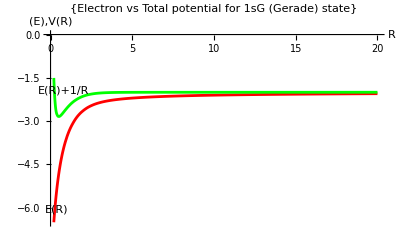

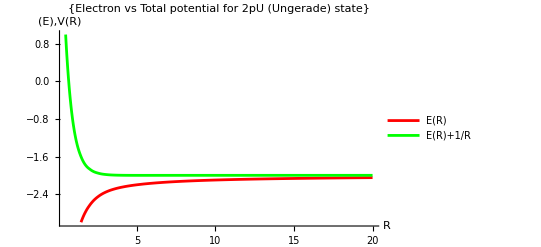

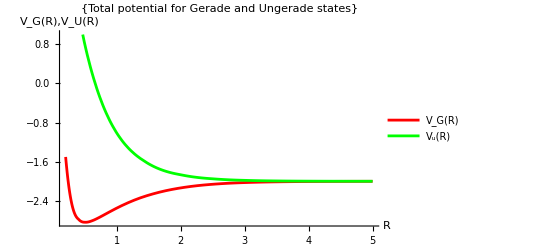

```mathematica
Plot[{eG[x],eGTotal[x]},{x,0.2,20}, PlotStyle->{Red,Green}, AxesLabel->{"R", "(E),V(R)"}, AxesOrigin->{0,0},PlotLabel->{"Electron vs Total potential for 1sG (Gerade) state"}, PlotLabels->Placed[{"E(R)","E(R)+1/R"},{Left}], PlotRange->Full]

eU = Interpolation[Transpose[{energiesUngerade[[All,1]],energiesGerade[[All,2]]}]];
eUTotal = Interpolation[Transpose[{energiesUngerade[[All,1]],energiesUngerade[[All,3]]}]];

Plot[{eU[x],eUTotal[x]},{x,0.2,20}, PlotStyle->{Red,Green},PlotRange->{1,-3}, AxesLabel->{"R", "(E),V(R)"}, AxesOrigin->{0,0},PlotLabel->{"Electron vs Total potential for 2pU (Ungerade) state"}, PlotLegends->{"E(R)","E(R)+1/R"}]


Plot[{eGTotal[x],eUTotal[x]},{x,0.2,5}, PlotStyle->{Red,Green},PlotRange->{1,-3}, AxesOrigin->{0,0},PlotLabel->{"Total potential for Gerade and Ungerade states"}, PlotLegends->{"V_G(R)","V_u(R)"}, AxesLabel->{"R", "V_G(R),V_U(R)"}]
```